# Computational explorations in modern number theory : the Green–Tao theorem and the abc conjecture

## Hiroyuki Chihara University of the Ryukyus Okinawa Island, Japan

### Prime numbers

Let us show you primes up to 1000.

```mathematica
(* Prime umbers up to 1000*)
Table[Prime[i],{i,1,168}]
```

{2,3,5,7,11,13,17,19,23,29,31,37,41,43,47,53,59,61,67,71,73,79,83,89,97,101,103,107,109,113,127,131,137,139,149,151,157,163,167,173,179,181,191,193,197,199,211,223,227,229,233,239,241,251,257,263,269,271,277,281,283,293,307,311,313,317,331,337,347,349,353,359,367,373,379,383,389,397,401,409,419,421,431,433,439,443,449,457,461,463,467,479,487,491,499,503,509,521,523,541,547,557,563,569,571,577,587,593,599,601,607,613,617,619,631,641,643,647,653,659,661,673,677,683,691,701,709,719,727,733,739,743,751,757,761,769,773,787,797,809,811,821,823,827,829,839,853,857,859,863,877,881,883,887,907,911,919,929,937,941,947,953,967,971,977,983,991,997}

### The Prime number theorem

The graphs of π(x) and x/log(x) are the following.

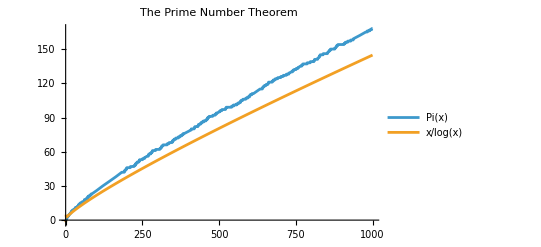

```mathematica
Plot[{PrimePi[x],x/Log[x]},{x,0,1000},PlotLabel->Style["The Prime Number Theorem",20, Blue],PlotLegends->Placed[{"Pi(x)","x/log(x)"},Left]]
```

### the Green - Tao Theorem

We observe arithmetic progressions of primes. Set “length” below.

```mathematica
(*Define initial terms*)
initialTerms={1,3,7,9};

(*Parameters*)
maxC=2000;
maxB=1000;
length=10;

(*Check arithmetic progression of primes*)
Do[Do[Do[terms=Table[a+10*b+10*(k-1)*c,{k,1,length}];
If[AllTrue[terms,PrimeQ],Print[terms]],{c,1,maxC}],{b,0,maxB}],{a,initialTerms}]
```

{1847,17807,33767,49727,65687,81647,97607,113567,129527,145487}

{199,409,619,829,1039,1249,1459,1669,1879,2089}

### The abc conjecture

We explore abc-triplets with small radical. Set “κ” below.

```mathematica
(* Define the radical *)
Rad[n_]:=Times@@Cases[FactorInteger[n],{x_,_}->x];
```

```mathematica
(* kappa*)
κ=1.4;
```

```mathematica
(* Examples of c ≥ rad(abc)^κ *)
Do[Do[If[GCD[a,b,a+b]==1&&a+b≥Rad[a*b*(a+b)]^κ,
Print["a=",a,",","b=",b,",","c=",a+b],Null],
{b,a+1,a+10000}],{a,1,1000}]
```

a=1,b=2400,c=2401

a=1,b=4374,c=4375

a=3,b=125,c=128

### The Collatz conjecture

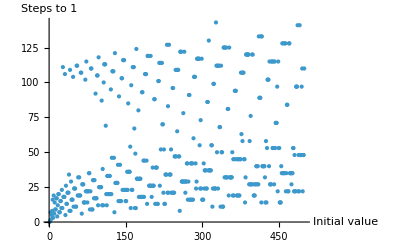

```mathematica
(* computing the stopping step for the Collatz sequence with the initial data m=1,...,500*)
collatz[n_]:=If[EvenQ[n],n/2,3 n+1]

stoppingTime[m_]:=Length[NestWhileList[collatz,m,#>1&]]-1

ListPlot[Table[{m,stoppingTime[m]},{m,1,500}],PlotStyle->PointSize[Small],AxesLabel->{"Initial value","Steps to 1"}]
```